```mathematica
Clear[Lx,Ly,A,
hopping2dx,hopping2dy,HoppingX2D,HoppingY2D,
cons,Cons,B]
```

```mathematica
Lx=30;
Ly=30;
A=Lx*Ly;
```

```mathematica
B=0.5;
```

```mathematica
(*--- We choose gauge A = (-By,0,0), hbar = 1, e = 1 ---*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sx2d[i_Integer,j_Integer]=0;

Do[Do[{sx2d[j+k Lx,j+1+k Lx]=-I/2 Exp[I B k],sx2d[j+1+k Lx,j+k Lx]=I/2 Exp[-I B k]},{j,1,Lx-1}],{k,0,Ly-1}]

SX2D=Table[sx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sx2dp[i_Integer,j_Integer]=0;

Do[{sx2dp[(k+1)Lx,1+k Lx]=-I/2,sx2dp[1+k Lx,(k+1)Lx]=I/2},{k,0,Ly-1}]

SX2DP=Table[sx2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sy2d[i_Integer,j_Integer]=0;

Do[Do[{sy2d[k Lx+j,(k+1)Lx+j]=-I/2,sy2d[(k+1)Lx+j,k Lx+j]=I/2},{j,1,Lx}],{k,0,Ly-2}]

SY2D=Table[sy2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sy2dp[i_Integer,j_Integer]=0;

Do[{sy2dp[(Ly-1)Lx+j,j]=-I/2,sy2dp[j,(Ly-1)Lx+j]=I/2},{j,1,Lx}]

SY2DP=Table[sy2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cx2d[i_Integer,j_Integer]=0;

Do[Do[{cx2d[j+k Lx,j+1+k Lx]=1/2 Exp[I B k],cx2d[j+1+k Lx,j+k Lx]=1/2 Exp[-I B k]},{j,1,Lx-1}],{k,0,Ly-1}]

CX2D=Table[cx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cx2dp[i_Integer,j_Integer]=0;

Do[{cx2dp[(1+k)Lx,1+k Lx]=1/2,cx2dp[1+k Lx,(1+k)Lx]=1/2},{k,0,Ly-1}]

CX2DP=Table[cx2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cy2d[i_Integer,j_Integer]=0;

Do[Do[{cy2d[k Lx+j,(k+1)Lx+j]=1/2,cy2d[(k+1)Lx+j,k Lx+j]=1/2},{j,1,Lx}],{k,0,Ly-2}]

CY2D=Table[cy2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cy2dp[i_Integer,j_Integer]=0;

Do[{cy2dp[(Ly-1)Lx+j,j]=1/2,cy2dp[j,(Ly-1)Lx+j]=1/2},{j,1,Lx}]

CY2DP=Table[cy2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*--------------- Lattice model for a constant matrix ---------------*)
```

```mathematica
cons[i_Integer, j_Integer]:=0

Do[{cons[i,i]=1},{i,1,A}]

Cons=Table[cons[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
hopping2dx[i_Integer,j_Integer]=0;

Do[Do[{hopping2dx[j+k Lx,j+1+k Lx]=1/2,hopping2dx[j+1+k Lx,j+k Lx]=1/2},{j,1,Lx-1}],{k,0,Ly-1}]

HoppingX2D=Table[hopping2dx[i,j],{i,1,A},{j,1,A}];
```

```mathematica
hopping2dy[i_Integer,j_Integer]=0;

Do[Do[{hopping2dy[j+k Lx,j+(k+1) Lx]=1/2 Exp[I B j],hopping2dy[j+(1+k) Lx,j+k Lx]=1/2 Exp[-I B j]},{j,1,Lx}],{k,0,Ly-2}]
HoppingY2D=Table[hopping2dy[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------- Lattice model for a constant matrix ---------------*)
```

```mathematica
cons[i_Integer, j_Integer]:=0

Do[{cons[i,i]=1},{i,1,A}]

Cons=Table[cons[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[σ0,σ1,σ2,σ3,HamiltonianQAHI,HamiltonianQAHI2]
```

```mathematica
σ0=PauliMatrix[0];
σ1=PauliMatrix[1];
σ2=PauliMatrix[2];
σ3=PauliMatrix[3];
```

```mathematica
HamiltonianQAHI=CX2D+CY2D;
```

```mathematica
(*--------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[val]
```

```mathematica
val=Eigenvalues[N[HamiltonianQAHI]];
```

```mathematica
val = Sort[val];
```

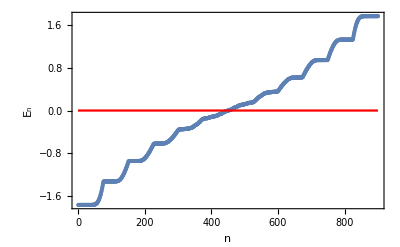

```mathematica
Show[ListPlot[val,Frame-> True,Axes-> False,PlotRange-> {{0,A},{Min[val],Max[val]}}],Plot[0,{x,0,A},PlotStyle-> Red],BaseStyle-> 14,FrameStyle-> Black,FrameLabel-> {"n","E_n"}]
```

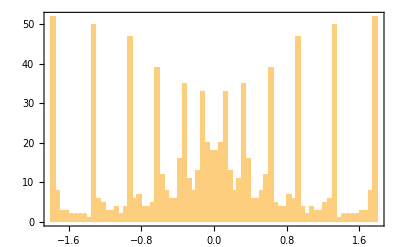

```mathematica
Show[Histogram[val,100],Frame-> True,FrameLabel-> {"E_n"}]
```

```mathematica
(*--------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
HamiltonianQAHI2=HoppingX2D+HoppingY2D;
```

```mathematica
Clear[val2]
```

```mathematica
val2=Eigenvalues[N[HamiltonianQAHI2]];
```

```mathematica
val2 = Sort[val2];
```

```mathematica
Show[ListPlot[val2,Frame-> True,Axes-> False,PlotRange-> {{0,A},{Min[val2],Max[val2]}}],Plot[0,{x,0,A},PlotStyle-> Red],BaseStyle-> 14,FrameStyle-> Black,FrameLabel-> {"n","E_n"}]
```

-Graphics-

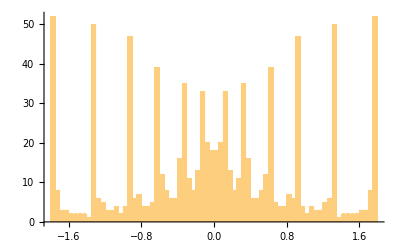

```mathematica
Histogram[val2,100]
```

```mathematica
(** Eigenvalues should be gauge invariant **)
```

```mathematica
Max[Abs[val-val2]]
```

1.19904×10^-14

```mathematica
Max[Abs[N[HamiltonianQAHI-HamiltonianQAHI2]]]
```

0.99999

```mathematica
Max[Abs[HoppingX2D-CX2D]]
```

√((1/2-Cos[22]/2)^2+Sin[22]^2/4)

```mathematica
Max[Abs[HoppingY2D-CY2D]]
```

√((-1/2+Cos[22]/2)^2+Sin[22]^2/4)